```mathematica
fft:= Module[{img, fft,fd,min,max,phase},img=RemoveAlphaChannel[Import["C:\\in.tiff"]];
fft=Fourier[ImageData[img]];
fft=RotateLeft[fft,Floor[Dimensions[fft] / 2]];
fd = Log[Abs[fft]-10.^-10];
min = N[Min[fd],12];
max = N[Max[fd],12];
fd = Rescale[fd]*256;
phase = ((Arg[fft]+Pi) / (2Pi))*256;
Export["C:\\fft.tiff",{"Image"->Image[fd,"Byte"],"ImageEncoding"->"LZW"},"Rules"];
Export["C:\\phase.tiff",{"Image"->Image[phase,"Byte"],"ImageEncoding"->"LZW"},"Rules"];
Export["C:\\fft.json",ExportString[{"koeff_lo"->min,"koeff_hi"->max},"JSON","Compact"->True]];
{}]
fft
```

{}

```mathematica
ifft:= Module[{fd,phase,koeffs, result},
fd = ImageData[Import["C:\\fft.tiff","Image"]];
koeffs = Association[ImportString[Import["C:\\fft.json"],"JSON"]];
phase = ImageData[Import["C:\\phase.tiff"]]*2*Pi - Pi;
result = (Exp[(fd+10.^-10)*(koeffs["koeff_hi"]-koeffs["koeff_lo"])-Abs[koeffs["koeff_lo"]]])*(Cos[phase] + Sin[phase] I);
result = Abs[InverseFourier[RotateRight[result,Floor[Dimensions[result] / 2]]]];
Export["C:\\out.tiff",{"Image"->Image[result*256,"Byte"],"ImageEncoding"->"ZIP"},"Rules"]
]
ifft
```

C:\out.tiff

```mathematica
img1=Import["C:\\phase.tiff"];
img2=Import["C:\\fft.tiff"];
cut`r=.25;
vert`bars=1;
ColorSpace1 =Association[Options[img1]][[Key[ColorSpace]]];
img1=ImageMultiply[img1,Graphics[{Black,Disk[{0,0},cut`r],White,Rectangle[{-1,-1},{1,-cut`r*vert`bars}],Rectangle[{-1,1},{1,cut`r*vert`bars}]},ImagePadding->None,ImageMargins->0,PlotRange->{{-1,1},{-1,1}},PlotRangePadding->None]];
img2=ImageMultiply[img2,Graphics[{Black,Disk[{0,0},cut`r],White,Rectangle[{-1,-1},{1,-cut`r*vert`bars}],Rectangle[{-1,1},{1,cut`r*vert`bars}]},ImagePadding->None,ImageMargins->0,PlotRange->{{-1,1},{-1,1}},PlotRangePadding->None]];
If[ColorSpace1=="Grayscale",
img1=ConformImages[{img1},ColorSpace->"Grayscale"][[1]];
img2=ConformImages[{img2},ColorSpace->"Grayscale"][[1]];
]
Export["C:\\phase.tiff",{"Image"->Image[img1,"Byte",ColorSpace->ColorSpace1],"ImageEncoding"->"ZIP"},"Rules"]
Export["C:\\fft.tiff",{"Image"->Image[img2,"Byte",ColorSpace->ColorSpace1],"ImageEncoding"->"ZIP"},"Rules"];
```

C:\phase.tiff

```mathematica
"C:\\fft.tiff"
```

C:\fft.tiff

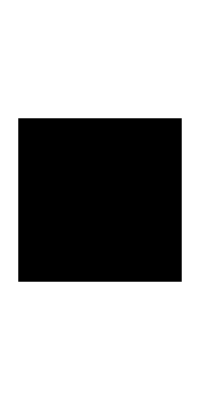

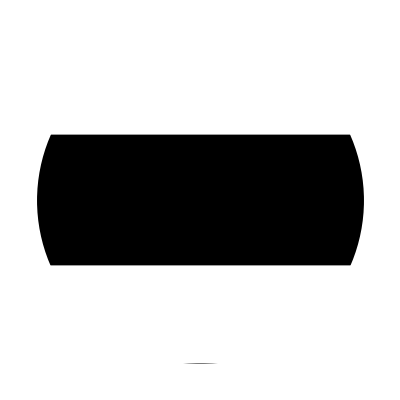

```mathematica
Graphics[{Black,Rectangle[{-1,-1}*.5,{1,1}*.5]},ImagePadding->None,ImageMargins->0,PlotRange->{-1,1},PlotRangePadding->None]
Graphics[{Black,Disk[{0,0},1],White,Rectangle[{-1,-1},{1,-.4}],Rectangle[{-1,1},{1,.4}]}]
```